# 雅可比矩阵的几何意义

```mathematica
StreamDensityPlot[{x^2,y^2},{x,-3,3},{y,-3,3}]
```

-Graphics-

```mathematica
J={{2x,0},{0,2y}};
StreamDensityPlot[J.{x^2,y^2},{x,-3,3},{y,-3,3}]
```

-Graphics-

```mathematica
雅可比矩阵
```

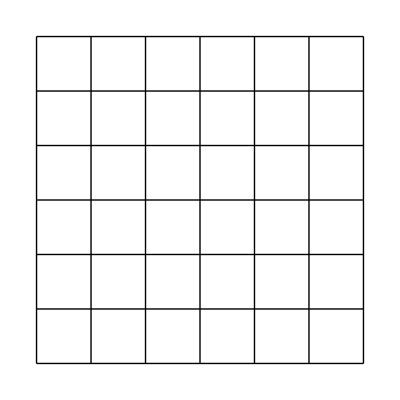

```mathematica
Graphics[{Line[Table[{{-3+d,-3},{-3+d,3}},{d,0,6}]],Line[Table[{{-3,-3+d},{3,-3+d}},{d,0,6}]]}]
```

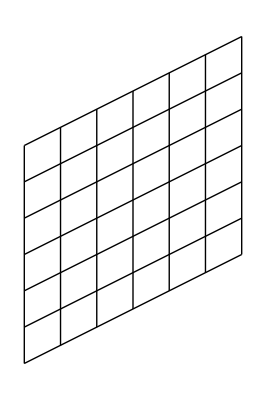

```mathematica
J={{2,0},{1,2}};
Graphics[{Line[Table[{J.{-3+d,-3},J.{-3+d,3}},{d,0,6}]],Line[Table[{J.{-3,-3+d},J.{3,-3+d}},{d,0,6}]]}]
```

```mathematica
DynamicModule[{r,pts,pts2,vs,o,f},r=10;pts=Table[{x,y},{x,-r,r},{y,-r,r}];vs={{1,0},{0,1}};o={0,0};f[p_]:={p[[1]]^2-p[[2]],p[[2]]^3}/5;LocatorPane[Dynamic[vs],Dynamic[pts2=Map[f,pts,{2}];Graphics[{(*Line[pts],Line[ptsᵀ],*)Magenta,Line[pts2],Line[pts2ᵀ],Arrow[{o,vs[[1]]}],Arrow[{o,vs[[2]]}]},PlotRange->r,GridLines->Automatic,GridLinesStyle->Directive[Orange,Dashed],Axes->True]]]]
```

```mathematica
Slider2D[Dynamic[{x,y}],{-2,2}]
sp=StreamDensityPlot[{x^2,y^2},{x,-3,3},{y,-3,3}];
Dynamic@Show[sp,J={{2x,0},{0,2y}};Graphics[{Line[Table[{J.{-3+d,-3},J.{-3+d,3}},{d,0,6}]],Line[Table[{J.{-3,-3+d},J.{3,-3+d}},{d,0,6}]]}]]
```

```mathematica
Slider2D[Dynamic[{x,y}],{-2,2}]
sp=StreamDensityPlot[{x^2,y^2},{x,-3,3},{y,-3,3}];
Dynamic@Show[sp,J={{2x,0},{0,2y}};Graphics[{Line[Table[{J.{-3+d,-3},J.{-3+d,3}},{d,0,6}]],Line[Table[{J.{-3,-3+d},J.{3,-3+d}},{d,0,6}]]}]]
```